```mathematica
small=RandomVariate[NormalDistribution[]]&/@Range[100]
large=10RandomVariate[NormalDistribution[]]&/@Range[100]
```

{-0.956754,-0.164579,0.667201,-0.740509,0.453794,0.579743,0.59857,1.53887,-0.227214,0.145187,-1.97399,2.15296,1.88092,-0.16555,1.79633,0.0728376,1.37051,-1.06851,-0.522759,0.205475,-0.384074,-0.943971,-0.0352782,0.429815,-0.452607,0.41671,0.692917,0.186282,-1.20451,-1.17994,-0.479962,-0.150208,-1.18172,0.224014,-1.29869,-1.2161,1.81172,-1.93169,-0.888708,-0.01508,-0.530897,0.711357,-0.996691,-0.249694,0.353572,-0.432226,2.84426,0.320878,-0.0651873,0.324225,0.647323,-1.38824,-0.0622931,0.36043,-0.0515042,-0.353736,0.536851,1.07478,-1.43001,0.0146365,-1.43188,-0.661794,-0.574112,0.0751364,0.658468,0.572992,1.30331,0.894426,-0.700611,-1.73995,0.254002,0.349995,-0.305452,0.23635,-0.0573873,-0.631085,0.413967,1.00215,-1.58601,0.311668,0.161072,0.975082,1.43328,1.25797,0.74291,0.622182,0.696128,-1.17029,-1.96611,-0.358078,1.17589,-2.79465,-0.703995,0.0953866,2.16571,-1.31961,1.0461,-2.66896,0.908597,-0.160706}

{13.4899,14.6663,6.89732,5.97366,-5.95632,6.358,-1.24285,13.686,3.78425,3.97476,-0.556587,-6.12287,11.9611,10.5405,6.73397,4.21154,-6.36844,-2.28174,0.241697,-4.1117,3.22054,-3.96595,-11.3464,0.753331,2.99441,4.25274,-0.562564,1.89457,-9.54426,8.72594,-14.4783,4.63955,0.896603,13.0457,6.35175,-4.46363,9.81386,-11.6081,17.8516,5.36569,-6.52119,-6.45347,22.8648,-11.0595,-8.808,4.13629,-8.11432,-32.3978,-6.42543,13.6014,16.8967,0.0108357,-6.15338,-15.4626,-20.9155,10.6273,-14.8721,-19.9772,1.93872,6.58917,11.139,-0.325562,0.257189,10.5998,-4.89162,3.21119,-7.6345,-1.57965,9.4827,-4.1566,-16.3286,6.61478,-3.47441,-10.8487,14.3059,11.1274,-9.58629,-3.09547,21.7199,3.20583,-14.641,-20.735,-5.75884,4.55619,-2.11356,10.482,-1.29518,9.40481,-1.55171,-15.5368,-4.24596,8.22485,5.17486,6.47469,5.83313,-7.39017,-5.69917,15.3936,4.77889,-7.99994}

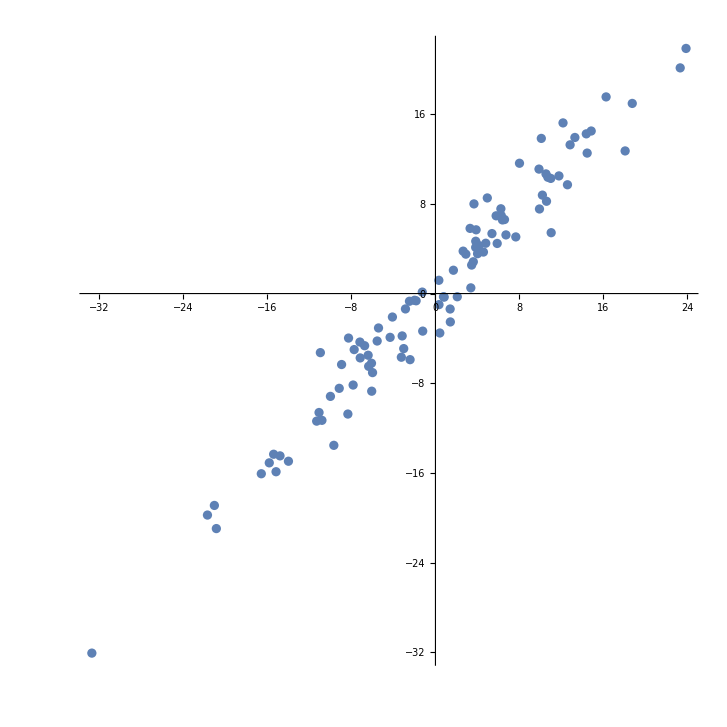

```mathematica
ListPlot[Transpose[{large-small,small+large}],AspectRatio->1,PlotRange->All]
```